```mathematica
statement1  =Simplify(ForAll[p,p⇒ q])
```

Simplify ∀_p(p⇒q)

```mathematica
Simplify[ForAll[p,p⇒p]]
```

True

```mathematica
p
```

p

```mathematica
TautologyQ[statement1 ⇒( p ⇒(p && q))]
```

False

```mathematica
!statement1
```

∃_p!(p⇒q)

```mathematica
TautologyQ[ForAll[x, P[x] && Q[x]] ⧦ (ForAll[x, P[x]] && ForAll[x,Q[x]])]
```

False

```mathematica
TautologyQ[(p && q ) ⧦ !(!p || !q)]
```

True

```mathematica
proof = FindEquationalProof[a==c,{a==b,b==c}]
```

ProofObject[…]

```mathematica
proof[%]
```

proof[ProofObject[…]]

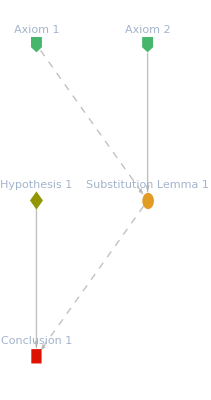

```mathematica
proof["ProofNotebook"]
```

```mathematica
Clear[P,Q]
```

```mathematica
proof2 = FindEquationalProof[ForAll[x, P[x] && Q[x]] ⧦ (ForAll[x, P[x]] && ForAll[x,Q[x]]),"BooleanAxioms"]
```

ProofObject[…]

```mathematica
proof2["ProofNotebook"]
```

Axiom 1
We are given that:
∀_{a,b}a⊗b==b⊗a
Axiom 2
We are given that:
∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c
Axiom 3
We are given that:
∀_{a,b}a⊕b⊗b̄==a
Axiom 4
We are given that:
∀_{a,b}a⊗(b⊕b̄)==a
Axiom 5
We are given that:
∀_{a,b}a⊕b==b⊕a
Axiom 6
We are given that:
∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)
Hypothesis 1
We would like to show that:
∀_x P[x]&&∀_x Q[x]⧦∀_x(P[x]&&Q[x])
Equationalized Axiom 1
We generate the ''equationalized'' axiom:
a==(a&&(b||!b))
Equationalized Axiom 2
We generate the ''equationalized'' axiom:
(a||b)==(b||a)
Equationalized Axiom 3
We generate the ''equationalized'' axiom:
(a&&b)==(b&&a)
Equationalized Hypothesis 1
We generate the ''equationalized'' hypothesis:
(c1||!c1)==((!(P[x]&&Q[x])||(P[x]&&Q[x]))&&(!(P[x]&&Q[x])||(P[x]&&Q[x])))
Critical Pair Lemma 1
The following expressions are equivalent:
((a||!a)&&b)==b
Proof
Note that the input for the rule:
a_&&b_<->b_&&a_
contains a subpattern of the form:
a_&&b_
which can be unified with the input for the rule:
a_&&(b_||!b_)→a
where these rules follow from Equationalized Axiom 3 and Equationalized Axiom 1 respectively.
Critical Pair Lemma 2
The following expressions are equivalent:
(a||!a)==(b||!b)
Proof
Note that the input for the rule:
(a_||!a_)&&b_→b
contains a subpattern of the form:
(a_||!a_)&&b_
which can be unified with the input for the rule:
a_&&(b_||!b_)→a
where these rules follow from Critical Pair Lemma 1 and Equationalized Axiom 1 respectively.
Substitution Lemma 1
It can be shown that:
(c1||!c1)==((!(P[x]&&Q[x])||(P[x]&&Q[x]))&&((P[x]&&Q[x])||!(P[x]&&Q[x])))
Proof
We start by taking Equationalized Hypothesis 1, and apply the substitution:
a_||b_→b||a
which follows from Equationalized Axiom 2.
Substitution Lemma 2
It can be shown that:
(c1||!c1)==(((P[x]&&Q[x])||!(P[x]&&Q[x]))&&((P[x]&&Q[x])||!(P[x]&&Q[x])))
Proof
We start by taking Substitution Lemma 1, and apply the substitution:
a_||b_→b||a
which follows from Equationalized Axiom 2.
Substitution Lemma 3
It can be shown that:
(c1||!c1)==((P[x]&&Q[x])||!(P[x]&&Q[x]))
Proof
We start by taking Substitution Lemma 2, and apply the substitution:
a_&&(b_||!b_)→a
which follows from Equationalized Axiom 1.
Substitution Lemma 4
It can be shown that:
(Q[x]||!Q[x])==((P[x]&&Q[x])||!(P[x]&&Q[x]))
Proof
We start by taking Substitution Lemma 3, and apply the substitution:
a_||!a_→Q[x]||!Q[x]
which follows from Critical Pair Lemma 2.
Conclusion 1
We obtain the conclusion:
(Q[x]||!Q[x])==(Q[x]||!Q[x])
Proof
Take Substitution Lemma 4, and apply the substitution:
a_||!a_→Q[x]||!Q[x]
which follows from Critical Pair Lemma 2.